```mathematica
lst=Table[i*10,{i,50}] (*returns {10,20,30,..,480,490,500}*)
lst[[1]] (*returns 10*)
lst[[10]] (*returns 100*)
lst[[1;;10]] (*returns {10,20,30,40,50,60,70,80,90,100}*)
lst[[20;;30]] (*returns {200,210,220,..,280,290,300}*)
lst[[30;;]] (*returns {300,310,320,330,340,..,470,480,490,500}*)
lst[[;;]] (*gives the full list*)
```

{10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500}

10

100

{10,20,30,40,50,60,70,80,90,100}

{200,210,220,230,240,250,260,270,280,290,300}

{300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500}

{10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500}

```mathematica
a=1;Which[a==1,x,a==2,b]
```

x

```mathematica
wf=Table[Sin[x],{x,0,Pi,Pi/24.0}][[1;;24]];
(*a model for the weekend,when people use more internet in the evening*)
wf2=Table[Sin[x]*Exp[x],{x,0,Pi,Pi/24.0}][[1;;24]];
wf2=wf2/Max[wf2];
```

```mathematica
data1=Partition[Riffle[ConstantArray[1,24],RandomReal[{0.5,1},24]*wf],2];
data2=Partition[Riffle[ConstantArray[1,24],RandomReal[{0.5,1},24]*wf],2];
(*simulate a weekend*)
data3=Partition[Riffle[ConstantArray[1,24],RandomReal[{0.5,1},24]*wf2],2];
data4=Partition[Riffle[ConstantArray[1,24],RandomReal[{0.5,1},24]*wf2],2];
```

```mathematica
SectorChart[data1]
SectorChart[{data1,data2}]
```

-Graphics-

-Graphics-

```mathematica
data1=Partition[Riffle[ConstantArray[1,24],RandomReal[{0.5,1},24]*wf],2];
```

```mathematica
SectorChart[data1]
```

-Graphics-

```mathematica
data=FinancialData["IBM",All];
```

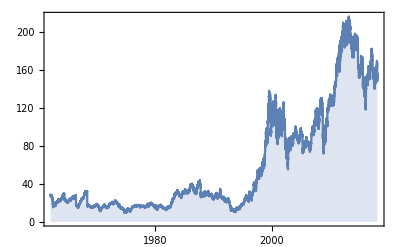

```mathematica
DateListPlot[data,Joined->True,Filling->Bottom]
```

```mathematica
data=FinancialData["Walmart",All];
```

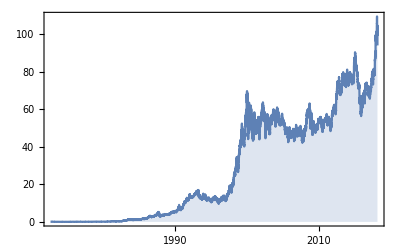

```mathematica
DateListPlot[data,Joined->True,Filling->Bottom]
```

```mathematica
data=FinancialData["Amazon",All];
```

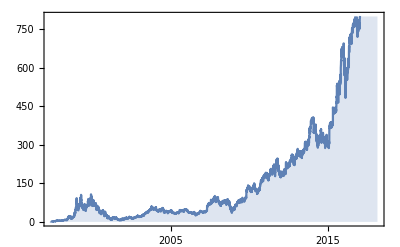

```mathematica
DateListPlot[data,Joined->True,Filling->Bottom]
```